```mathematica
Clear[a, b, c, d, f]
```

```mathematica
(* Sigmoidal equation #5 for Mar8, returns dose concentration given instrument response.  Asymptotes are 'f' on the left, and 'a+f' on the right. *)
```

```mathematica
sigmoidal[r_]:= a * (1+Exp[(b-r)/c])^-d+f
```

```mathematica
(* Invert the equation to obtain instrument response as a function of dose concentration. *)
```

```mathematica
Solve[t==sigmoidal[r], r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→b-c Log[-1+((-f+t)/a)^(-1/d)]}}

```mathematica
(* Set second derivative to zero to obtain dose concentration value for which instrument response is at its midpoint. *)
```

```mathematica
Solve[Simplify[sigmoidal''[r]==0], r]
```

{{r→b+c Log[d]}}

```mathematica
(* Example curve using coefficients obtained in the Excel Solver. *)
```

```mathematica
a=1.06 ;b=0.19; c=0.19; d=4; f=0
```

0

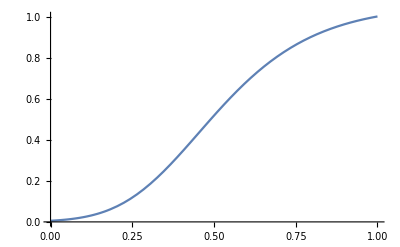

```mathematica
Plot[sigmoidal[r], {r, 0, 1}]
```